```mathematica
rule={n0->100,ζ->.4,A->5,B->5.05,α->14,β->126,k->4*.322};
a=-300;
b=300;
```

```mathematica
(* linear preferred and non-preferred force-velocity curves from force_nondim_exp_and_linear.nb. preferred direction negative velocity *)
fPref[U_]=-(k n0 α (U+A β))/(β (α+β))/.rule;
fNonPref[U_]=-(k n0 α (U+A β-ⅇ^(((A-B) β)/U) (U+B β)))/(β (α-ⅇ^(((A-B) β)/U) α+β))/.rule;
```

```mathematica
fVDown[U_]:=If[U>0,fNonPref[U],fPref[U]];
fMotors[U_]:=fVDown[U]-fVDown[-U];
```

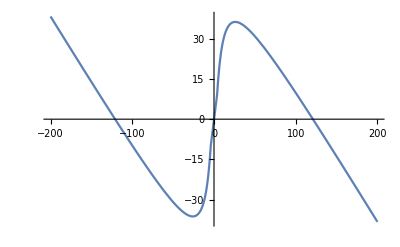

```mathematica
Plot[fMotors[U]-ζ U/.rule,{U,-200,200}]
```

```mathematica
ps[x_?NumericQ,σ_?NumericQ]:=1/σ^2 Exp[2 NIntegrate[(fMotors[U]-ζ U)/σ^2/.rule,{U,a,x}]]/.rule;
n[s_?NumericQ]:=NIntegrate[ps[x,s],{x,a,b}]
```

```mathematica
n[50]
```

52.8195

```mathematica
ps[100,50]
```

0.188646

```mathematica
(* separate the normalization so it only evaluates once in the plot *)
n1=n[10];
```

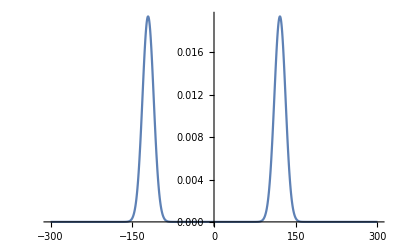

```mathematica
Plot[ps[x,10]/n1,{x,-300,300},PlotRange->All]
```

```mathematica
(* load histogram data from python *)
xList=Import[ToFileName[{NotebookDirectory[],".."},"bins.csv"]];
yList=Import[ToFileName[{NotebookDirectory[],".."},"counts.csv"]];
```

```mathematica
xList=Drop[Flatten[xList],-1];
yList=Flatten[yList];
```

```mathematica
Length[xList]
Length[yList]
```

40

40

```mathematica
data =Transpose[{xList,yList}];
```

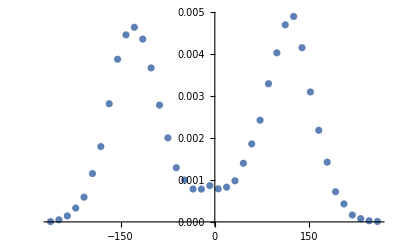

```mathematica
ListPlot[data]
```

```mathematica
(* fit sigma parameter of function to the above data *)
model=  ps[x,σ]/n[σ];
```

```mathematica
(*fit=FindFit[data,{model,{σ>40}},{σ},x]*)
```